```mathematica
one = {{1},{I}}
```

{{1},{ⅈ}}

```mathematica
one//MatrixForm
```

(1
ⅈ)

```mathematica
onedagger=ConjugateTranspose[one]
```

{{1,-ⅈ}}

```mathematica
onedagger//MatrixForm
```

(1 | -ⅈ)

```mathematica
two={{1},{-I}}
```

{{1},{-ⅈ}}

```mathematica
two//MatrixForm
```

(1
-ⅈ)

```mathematica
twodagger=ConjugateTranspose[two]
```

{{1,ⅈ}}

```mathematica
twodagger//MatrixForm
```

(1 | ⅈ)

```mathematica
b={{-I},{0},{I}}
```

{{-ⅈ},{0},{ⅈ}}

```mathematica
bdagger=ConjugateTranspose[b]
```

{{ⅈ,0,-ⅈ}}

```mathematica
omega = {{0,hbar/√2,0},{hbar/√2,0,hbar/√2},{0,hbar/√2,0}}
```

{{0,hbar/(√2),0},{hbar/(√2),0,hbar/(√2)},{0,hbar/(√2),0}}

```mathematica
omega // MatrixForm
```

(0 | hbar/(√2) | 0
hbar/(√2) | 0 | hbar/(√2)
0 | hbar/(√2) | 0)

```mathematica
Eigenvalues[omega]
```

{-hbar,hbar,0}

```mathematica
Eigenvectors[omega]
```

{{1,-√2,1},{1,√2,1},{-1,0,1}}

```mathematica
u = {{1/2,-√2/2,1/2},{-1/√2,0,1/√2},{1/2,√2/2,1/2}}
```

{{1/2,-1/(√2),1/2},{-1/(√2),0,1/(√2)},{1/2,1/(√2),1/2}}

```mathematica
u//MatrixForm
```

(1/2 | -1/(√2) | 1/2
-1/(√2) | 0 | 1/(√2)
1/2 | 1/(√2) | 1/2)

```mathematica
udagger = ConjugateTranspose[u]
```

{{1/2,-1/(√2),1/2},{-1/(√2),0,1/(√2)},{1/2,1/(√2),1/2}}

```mathematica
udagger//MatrixForm
```

(1/2 | -1/(√2) | 1/2
-1/(√2) | 0 | 1/(√2)
1/2 | 1/(√2) | 1/2)

```mathematica
udagger.u
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
ucorrect=udagger.u//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
udagger.omega.u
```

{{-hbar,0,0},{0,0,0},{0,0,hbar}}

```mathematica
omegavalues = udagger.omega.u//MatrixForm
```

(-hbar | 0 | 0
0 | 0 | 0
0 | 0 | hbar)

```mathematica
u1={{1/2,-√2/2,1/2},{1/√2,0,-1/√2},{1/2,1/√2,1/2}}
```

{{1/2,-1/(√2),1/2},{1/(√2),0,-1/(√2)},{1/2,1/(√2),1/2}}

```mathematica
u1//MatrixForm
```

(1/2 | -1/(√2) | 1/2
1/(√2) | 0 | -1/(√2)
1/2 | 1/(√2) | 1/2)

```mathematica
u1dagger = ConjugateTranspose[u1]
```

{{1/2,1/(√2),1/2},{-1/(√2),0,1/(√2)},{1/2,-1/(√2),1/2}}

```mathematica
u1dagger//MatrixForm
```

(1/2 | 1/(√2) | 1/2
-1/(√2) | 0 | 1/(√2)
1/2 | -1/(√2) | 1/2)

```mathematica
u1.u1dagger//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
u1correct = u1.u1dagger
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
u1correct//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
omegau1values= u1dagger.omega.u1
```

{{hbar,0,0},{0,0,0},{0,0,-hbar}}

```mathematica
omegau1values//MatrixForm
```

(hbar | 0 | 0
0 | 0 | 0
0 | 0 | -hbar)

```mathematica
omega.ucorrect
```

{{0,hbar/(√2),0},{hbar/(√2),0,hbar/(√2)},{0,hbar/(√2),0}}.(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
omega3 = {{hbar,0,0},{0,0,0},{0,0,-hbar}}
```

{{hbar,0,0},{0,0,0},{0,0,-hbar}}

```mathematica
omega3//MatrixForm
```

(hbar | 0 | 0
0 | 0 | 0
0 | 0 | -hbar)

```mathematica
udagger.omega3.u
```

{{0,-hbar/(√2),0},{-hbar/(√2),0,-hbar/(√2)},{0,-hbar/(√2),0}}

```mathematica
omega3values = udagger.omega3.u//MatrixForm
```

(0 | -hbar/(√2) | 0
-hbar/(√2) | 0 | -hbar/(√2)
0 | -hbar/(√2) | 0)

```mathematica
omega1 = {{0,-I.hbar/√2,0},{I.hbar/√2,0,-I.hbar/√2},{0,I.hbar/√2,0}}
```

{{0,-(ⅈ.hbar)/(√2),0},{(ⅈ.hbar)/(√2),0,-(ⅈ.hbar)/(√2)},{0,(ⅈ.hbar)/(√2),0}}

```mathematica
omega1//MatrixForm
```

```mathematica
({{0, -(ⅈ.hbar)/(√2), 0}, {(ⅈ.hbar)/(√2), 0, -(ⅈ.hbar)/(√2)}, {0, (ⅈ.hbar)/(√2), 0}})
```

{{0,-(ⅈ.hbar)/(√2),0},{(ⅈ.hbar)/(√2),0,-(ⅈ.hbar)/(√2)},{0,(ⅈ.hbar)/(√2),0}}

```mathematica
(omega.omega1)
```

{{(hbar ⅈ.hbar)/2,0,-1/2 hbar ⅈ.hbar},{0,0,0},{(hbar ⅈ.hbar)/2,0,-1/2 hbar ⅈ.hbar}}

```mathematica
omega1.omega
```

{{-1/2 hbar ⅈ.hbar,0,-1/2 hbar ⅈ.hbar},{0,0,0},{(hbar ⅈ.hbar)/2,0,(hbar ⅈ.hbar)/2}}

```mathematica
commute = {{hbar ⅈ.hbar,0,0},{0,0,0},{0,0,-hbar ⅈ.hbar}}
```

{{hbar ⅈ.hbar,0,0},{0,0,0},{0,0,-hbar ⅈ.hbar}}

```mathematica
commute//MatrixForm
```

(hbar ⅈ.hbar | 0 | 0
0 | 0 | 0
0 | 0 | -hbar ⅈ.hbar)

```mathematica
plushbar = {1/2,1/√2,1/2}
```

{1/2,1/(√2),1/2}

```mathematica
plushbar//MatrixForm
```

(1/2
1/(√2)
1/2)

```mathematica
plushardagger=ConjugateTranspose[plushbar]
```

ConjugateTranspose::nmtx: The first two levels of {1/2,1/(√2),1/2} cannot be transposed.

ConjugateTranspose[{1/2,1/(√2),1/2}]

```mathematica
minushbar = { 1/2,-1/√2,1/2}
```

{1/2,-1/(√2),1/2}

```mathematica
minushbar//MatrixForm
```

(1/2
-1/(√2)
1/2)

```mathematica
psi = 1/√2 minushbar - i/2 plushbar
```

{1/(2 √2)-i/4,-1/2-i/(2 √2),1/(2 √2)-i/4}

```mathematica
omega.psi
```

{(hbar (-1/2-i/(2 √2)))/(√2),√2 hbar (1/(2 √2)-i/4),(hbar (-1/2-i/(2 √2)))/(√2)}

```mathematica
psidagger = ConjugateTranspose[psi]
```

ConjugateTranspose::nmtx: The first two levels of {1/(2 √2)-i/4,-1/2-i/(2 √2),1/(2 √2)-i/4} cannot be transposed.

ConjugateTranspose[{1/(2 √2)-i/4,-1/2-i/(2 √2),1/(2 √2)-i/4}]

```mathematica
psidagger.omega.psi
```

ConjugateTranspose[{1/(2 √2)-i/4,-1/2-i/(2 √2),1/(2 √2)-i/4}].{(hbar (-1/2-i/(2 √2)))/(√2),√2 hbar (1/(2 √2)-i/4),(hbar (-1/2-i/(2 √2)))/(√2)}

```mathematica
k[e_,u_]:=Sqrt[2*m*(u-e)/hbar^2]
```

```mathematica
κ[e_,u_]:=Sqrt[2*m*e/hbar^2]
```

```mathematica
k[e,u]
```

√2 √((m (-e+u))/hbar^2)

```mathematica
κ[e,u]
```

√2 √((e m)/hbar^2)

```mathematica
ψI[e_,u_,x_]:=cC*Exp[I*k[e,u]*x]
```

```mathematica
ψII[e_,u_,x_]:=bB*Exp[-κ[e,u]*x]
```

```mathematica
ψI[e,u,x]
```

cC ⅇ^(ⅈ √2 √((m (-e+u))/hbar^2) x)

```mathematica
ψII[e,u,x]
```

bB ⅇ^(-√2 √((e m)/hbar^2) x)

```mathematica
D[ψI[e,u,x],x]
```

ⅈ √2 cC ⅇ^(ⅈ √2 √((m (-e+u))/hbar^2) x) √((m (-e+u))/hbar^2)

```mathematica
ψIp[e_,u_,x_]:=ⅈ √2 cC ⅇ^(ⅈ √2 √((m (-e+u))/hbar^2) x) √((m (-e+u))/hbar^2)
```

```mathematica
ψIp[e,u,x]
```

ⅈ √2 cC ⅇ^(ⅈ √2 √((m (-e+u))/hbar^2) x) √((m (-e+u))/hbar^2)

```mathematica
D[ψII[e,u,x],x]
```

-√2 bB ⅇ^(-√2 √((e m)/hbar^2) x) √((e m)/hbar^2)

```mathematica
ψIIp[e_,u_,x_]:=-√2 bB ⅇ^(-√2 √((e m)/hbar^2) x) √((e m)/hbar^2)
```

```mathematica
ψIIp[e,u,x]
```

-√2 bB ⅇ^(-√2 √((e m)/hbar^2) x) √((e m)/hbar^2)

```mathematica
Solve[(ψIp[e,u,a]/ψI[e,u,a])-(ψIIp[e,u,a]/ψII[e,u,a])==0,cC]
```

{{}}

```mathematica
lhs[e_,u_]:=ψIp[e,u,a]/ψI[e,u,a]
```

```mathematica
lhs[e,u]
```

ⅈ √2 √((m (-e+u))/hbar^2)

```mathematica
rhs[e_,u_]:=ψIIp[e,u,a]/ψII[e,u,a]
```

```mathematica
rhs[e,u]
```

-√2 √((e m)/hbar^2)

```mathematica
hbar=197.32
```

197.32

```mathematica
m=938.
```

938.

```mathematica
a=2.0
```

2.

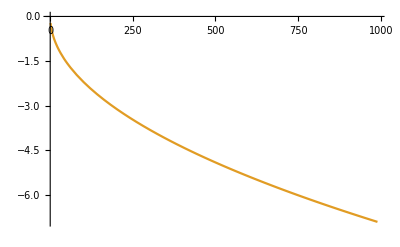

```mathematica
Plot[{lhs[e,1000], rhs[e,1000]},{e,1,990}]
```

```mathematica
Clear[hbar]
```